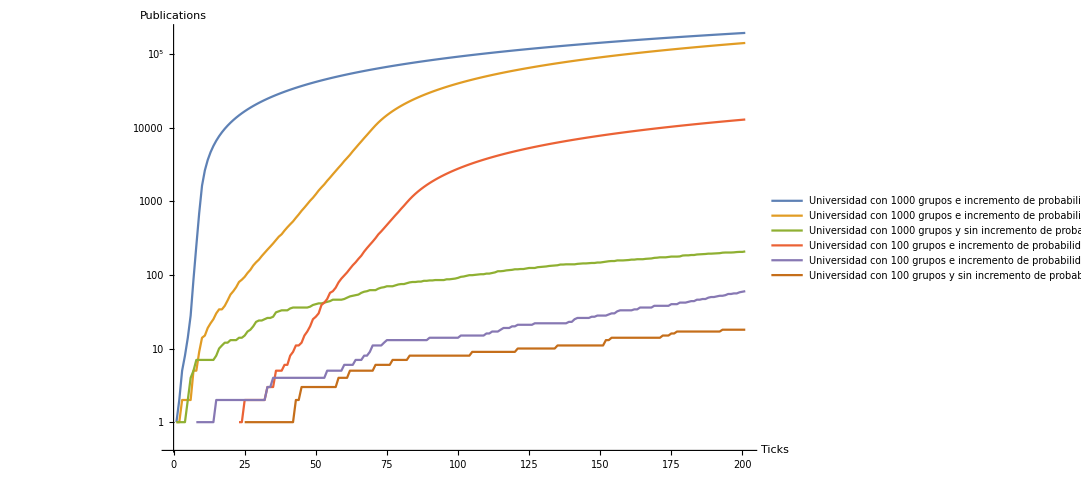

```mathematica
SetDirectory["/home/fabianact/NUEVOMODELO/PrimeraVersion"]; 
pub1G100= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub1-100-100-100-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub2G100= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub2-100-100-100-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub3G100= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub3-100-100-100-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub1G1000= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub1-1000-1000-1000-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub2G1000= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub2-1000-1000-1000-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub3G1000= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub3-1000-1000-1000-0.001-0.001-1.0E-4-0-100-curve.csv"];
                          plotPub = Show[ListLogPlot[{ pub1G1000, pub2G1000, pub3G1000, pub1G100, pub2G100, pub3G100 },ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "Universidad con 1000 grupos
 e incremento de probabilidad de 1.0E-3",  "Universidad con 1000 grupos
 e incremento de probabilidad de 1.0E-4",  "Universidad con 1000 grupos
 y sin incremento de probabilidad",  "Universidad con 100 grupos
 e incremento de probabilidad de 1.0E-3",  "Universidad con 100 grupos
 e incremento de probabilidad de 1.0E-4",  "Universidad con 100 grupos
 y sin incremento de probabilidad"},PlotRange->All]]
Export["total-curve.png",plotPub];
```